## Opakování na písemný test

1.)

Vytvořte funkci “vypocet” která bude mít 3 vstupní parametry : Min = 0, Max = 10, Krok = 0.2 (pro generování dat využíjte funkci Table). Výstup funkce bude obsahovat tabulku se  třemi sloupci “x”, “Sin(x)” a “Cos(x)”. Dalším výstupem bude graf průběhu funkcí Sin(x) a Cos(x) vykreslený pomocí funkce ListPlot z vygenerovaných dat. Ve funkci použijte lokální proměnné. Hlavička tabulky bude mít tvar :pro řádky vygenerujte číslo řádku za který vložite text “řádek”, k tomu lze využít funkce “StringJoin” a “ToString”. Pro sloupce využijte názvy “x”, “Sin(x)” a “Cos(x)”. Pro sestrojení obou grafů je nutno vybrat “x” a “y” souřadnici z vygenerovaných dat (sloupce). Tabulka i Graf budou formátovány dle výsledku níže.

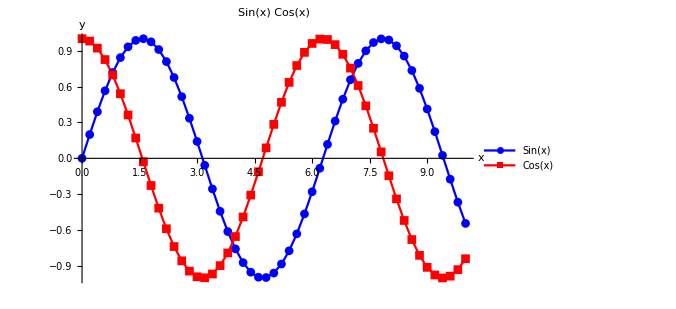
-Graphics-
 | x | Sin(x) | Cos(x)
1. řádek | 0. | 0. | 1.
2. řádek | 0.2 | 0.198669 | 0.980067
3. řádek | 0.4 | 0.389418 | 0.921061
4. řádek | 0.6 | 0.564642 | 0.825336
5. řádek | 0.8 | 0.717356 | 0.696707
6. řádek | 1. | 0.841471 | 0.540302
7. řádek | 1.2 | 0.932039 | 0.362358
8. řádek | 1.4 | 0.98545 | 0.169967
9. řádek | 1.6 | 0.999574 | -0.0291995
10. řádek | 1.8 | 0.973848 | -0.227202
11. řádek | 2. | 0.909297 | -0.416147
12. řádek | 2.2 | 0.808496 | -0.588501
13. řádek | 2.4 | 0.675463 | -0.737394
14. řádek | 2.6 | 0.515501 | -0.856889
15. řádek | 2.8 | 0.334988 | -0.942222
16. řádek | 3. | 0.14112 | -0.989992
17. řádek | 3.2 | -0.0583741 | -0.998295
18. řádek | 3.4 | -0.255541 | -0.966798
19. řádek | 3.6 | -0.44252 | -0.896758
20. řádek | 3.8 | -0.611858 | -0.790968
21. řádek | 4. | -0.756802 | -0.653644
22. řádek | 4.2 | -0.871576 | -0.490261
23. řádek | 4.4 | -0.951602 | -0.307333
24. řádek | 4.6 | -0.993691 | -0.112153
25. řádek | 4.8 | -0.996165 | 0.087499
26. řádek | 5. | -0.958924 | 0.283662
27. řádek | 5.2 | -0.883455 | 0.468517
28. řádek | 5.4 | -0.772764 | 0.634693
29. řádek | 5.6 | -0.631267 | 0.775566
30. řádek | 5.8 | -0.464602 | 0.88552
31. řádek | 6. | -0.279415 | 0.96017
32. řádek | 6.2 | -0.0830894 | 0.996542
33. řádek | 6.4 | 0.116549 | 0.993185
34. řádek | 6.6 | 0.311541 | 0.950233
35. řádek | 6.8 | 0.494113 | 0.869397
36. řádek | 7. | 0.656987 | 0.753902
37. řádek | 7.2 | 0.793668 | 0.608351
38. řádek | 7.4 | 0.898708 | 0.438547
39. řádek | 7.6 | 0.96792 | 0.25126
40. řádek | 7.8 | 0.998543 | 0.0539554
41. řádek | 8. | 0.989358 | -0.1455
42. řádek | 8.2 | 0.940731 | -0.339155
43. řádek | 8.4 | 0.854599 | -0.519289
44. řádek | 8.6 | 0.734397 | -0.67872
45. řádek | 8.8 | 0.584917 | -0.811093
46. řádek | 9. | 0.412118 | -0.91113
47. řádek | 9.2 | 0.22289 | -0.974844
48. řádek | 9.4 | 0.0247754 | -0.999693
49. řádek | 9.6 | -0.174327 | -0.984688
50. řádek | 9.8 | -0.366479 | -0.930426
51. řádek | 10. | -0.544021 | -0.839072

## Obsah hodiny

Funkce Plot3D

Pro vykreslení grafů dvou proměných využívá Mathematica funkci Plot3D. Tato funkce opět nabízí široké možnosti. U funkce Plot3D[] musíme zadat výraz pro výpočet třetí souřadnice, a pak rozsah souřadnice podle předpisu Plot3D[f,{x,x_min,x_max},{y,y_min,y_max}]. Mathematica vypočte funkci v ose z a následně funkci zobrazí z(x,y) = √(100-x^2-y^2) v rozsahu x a y od -10 do 10. U 3D grafů v Mathematice můžeme využít levé tlačítko k otáčení grafu.

```mathematica
Plot3D[√(100-x^2-y^2),{x,-10,10},{y,-10,10}]
```

-Graphics3D-

Změna počtu zobrazovaných bodů plochy (pro každou osu) - příkaz PlotPoints

```mathematica
Plot3D[√(100-x^2-y^2),{x,-10,10},{y,-10,10},
PlotPoints->100
]
```

-Graphics3D-

Výčet barev, které můžete využít. Pro získání kompletního výčtu barev lze využít paletu Color Schemes. (Palettes -> Color Schemes)

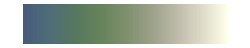
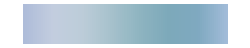
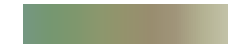
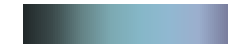
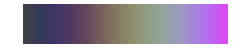
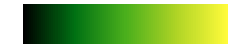
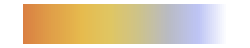
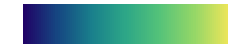

```mathematica
GraphicsGrid[Partition[ColorData[#,"Image"]&/@ColorData["Gradients"],3],ImageSize->300]
```

Vykreslení 3D grafu pomocí příkazu ColorFunction a přidání legendy grafu.

```mathematica
Plot3D[√(100-x^2-y^2),{x,-10,10},{y,-10,10},
ColorFunction->"BlueGreenYellow",
PlotLegends->Automatic
]
```

-Graphics3D-

Vykreslování 3D grafu podle osy “z”  (barvy pro osy “x” a ”y” jsou nastaveny staticky)	.

```mathematica
graf1=Plot3D[√(100-x^2-y^2),{x,-10,10},{y,-10,10},ColorFunction->Function[{x,y,z},Hue[z]]
]
```

-Graphics3D-

Graf nemusí být vykreslován pouze pomocí barvy ale také pomocí vrstevnic.

```mathematica
Plot3D[√(100-x^2-y^2),{x,-10,10},{y,-10,10},
PlotTheme->"Web"
]
```

-Graphics3D-

Vybarvení jednotlivých polích 3D grafu pomocí příkazu MeshShading. Výsledný graf je také doplněn o popisky os AxesLabel a název grafu PlotLabel.

```mathematica
Plot3D[√(100-x^2-y^2),{x,-10,10},{y,-10,10},
MeshShading->{{Blue,Purple},{Green,Orange}},
AxesLabel->{"osa x","osa y","osa z"},
PlotLabel->"Graf"
]
```

-Graphics3D-

Pomocí příkazu PlotStyle můžeme definovat barvu pro každý vykreslovaný graf zvlášť.

```mathematica
Plot3D[{Sin[x],Cos[x]},{x,0,2Pi},{y,0,2Pi},
PlotStyle->{Orange,Purple}
]
```

-Graphics3D-

Nastavení výchozího pohledu na zobrazený graf ze předu (Front), z vrchu (Top).

```mathematica
Plot3D[Sin[x ]^2-Cos[y]^2,{x,0,5},{y,0,3},
ViewPoint->Front
]
```

-Graphics3D-

Nastavení výchozího pohledu na zobrazený graf pomocí souřadnic.

```mathematica
Plot3D[Sin[x ]^2-Cos[y]^2,{x,0,5},{y,0,3},
ViewPoint->{3,-5,3}
]
```

-Graphics3D-

Využití mřížky pro 3D graf.

```mathematica
Plot3D[Sin[x ]^2-Cos[y]^2,{x,0,5},{y,0,3},
FaceGrids->All
]
```

-Graphics3D-

Definování mřížky jen z vybraných stran pomocí příkazu FaceGrids. Nastavení stylů vykreslované mřížky pomocí příkazu FaceGridsStyle.

```mathematica
Plot3D[Sin[x ]^2-Cos[y]^2,{x,0,5},{y,0,3},
FaceGrids->{{0,0,-1},{0,1,0}},
FaceGridsStyle->Directive[Blue,Dotted,Thickness@0.007]
]
```

-Graphics3D-

Vykreslování 3D grafu můžeme měnit pomocí několika příkazů. 
Příkaz Background mění barevné pozadí grafu. 
Příkaz BoundaryStyle mění styl hranice grafu. 
Příkaz Filling se využívá k vyplnění plochy kolem grafu. 
Pomocí příkazu FillingStyle můžeme měnit styly (Filling) barva atd. 
Příkaz Mesh určuje měřítko mřížky na grafu. 
Příkaz MeshStyle určuje styl mřížky. 
Pomocí příkazu PlotLegend můžeme nastavit popis legendy. 
Příkaz Opacity určuje průhlednost grafu.

```mathematica
Plot3D[Sin[x ]^2-Cos[y]^2,{x,0,5},{y,0,3},
Background->Gray,
BoundaryStyle->Directive[Red,Thick],
Filling->Bottom,
FillingStyle->Purple,
Mesh->5,
MeshStyle->Red,
PlotLegends->{"graf"},
PlotStyle->Opacity[0.7]
]
```

-Graphics3D-

Funkce Listplot3D

Funkce ListPlot3D je obdobná jako funkce Plot3D. Jako vstup můžeme využít několik zadaných vektorů nebo vygenerované data pomocí funkce Table. Z následujícího grafu vidímě to, že pomocí jednotlivých vektorů definujeme souřadnici “Z”. Matice hodnot souřadnice “Z” je pravidelně vykreslena v osách “X” a “Y”.

```mathematica
ListPlot3D[{{1,1,1,1},{1,2,1,2},{1,1,3,1},{1,2,1,4}},Mesh->All]
```

-Graphics3D-

```mathematica
data=Table[{x^2,x^3},{x,0,5,0.5}];
```

```mathematica
ListPlot3D[data,Mesh->All]
```

-Graphics3D-

Pro následující funkci ListPlot3D jsou vygenerovány data pomocí funkce Table, kde je využito celočíselného dělení pomoci funkce Mod. Formátování je podobné jako u funkce Plot3D.

```mathematica
graf2=ListPlot3D[
Table[Mod[x,y],{x,1,20},{y,1,20}],
Background->Gray,
BoundaryStyle->Directive[Red,Thick],
Filling->Bottom,
FillingStyle->Purple,
Mesh->5,
MeshStyle->Red,
PlotLegends->{"graf"},
PlotStyle->Opacity[0.7]
]
```

-Graphics3D-

Pomocí funkce show lze jednotlivé grafy slučovat.

```mathematica
Show[graf2,graf1]
```

-Graphics3D-

## Samostatné úkoly

1.)

Vytvořte 3D graf podle funkce Sin(2x)-Cos(2x-y)+Sin(x^3) v intervalu x ϵ (0,3) a y ϵ (0,3). 
	a) Vytvořte popisky os a název grafu. Navíc nastavte jemnost vykreslované sítě na 50, pro vyhlazení grafu.
	b) Nastavte úhel pohledu na (1,2,1).
	c) Vytvořte síť (mřížku) jenom pod vykreslovaným grafem.
	d) Výsledný graf vybarvěte barvami v závislosti na ose z.

-Graphics3D-